# Pieces of Art appreciated with Wolfram Language Machine Learning

Applying machine learning and the Wolfram Language functionality to learn about five of the most famous painting artist in history.

Diego Gutierrez Coronel, Jun. 24,  2018

Mathematica and the Wolfram Language is known for being a symbolic language that also works well for plotting and visualisation. However it can be used for much more, with a simple but broad functionality for Machine Learning. It can be very useful to analyze data, simulate processes, either scientific or mathematical, and even develop software for different applications. Art appreciation and categorization can be though of as a subjective topic not related with computation. However, nowadays the tools developed by machine learning have already been used to study art history, style, among others.

## From Renaissance to Post-Impressionism

We will apply some of the Machine Learning tools in the Wolfram Language to look at five different artist as shown in the list created below. Each one of the artist belonging to different periods of time and stylistic movements in art. Representing the Italian Renaissance is Sandro Botticelli, form the Baroque period is Spanish artist Diego Velázquez, and his famous compatriot Pablo Picasso, figure of the Cubistic style. Additionally we have Claude Monet and Vincent van Gogh from opposing movements, Impressionism and Post-Impressionism, respectively. With the Wolfram Language, this set of strings can be converted into real-world entities that can be used symbolically.

```mathematica
paintersList = {"Sandro Boticelli", "Diego Velazquez", "Claude Monet", "Vincent Van Gogh", "Picasso"}
Interpreter["Person"][#] & /@ paintersList
```

{Sandro Boticelli,Diego Velazquez,Claude Monet,Vincent Van Gogh,Picasso}

{Sandro Botticelli,Diego Velázquez,Claude Monet,Vincent van Gogh,Pablo Picasso}

These entities contain different properties and thus we can access information and various types of data from this symbolic expressions. Here we take a random sample of five famous paintings from Picasso. We can also check the number of “Notable Artworks” Images stored under Boticelli’s Entity.

```mathematica
EntityValue[RandomSample[LinguisticAssistant["NotableArtworks"], 3], "Image"]
Length[Cases[EntityValue[EntityList[LinguisticAssistant["NotableArtworks"]],"Image"],_Image]]
```

{-Graphics-,-Graphics-,-Graphics-}

52

With the following code we assign a list of 5 lists of notable paintings from each of the artist presented.

```mathematica
paintingImages=Cases[EntityValue[
RandomSample[Interpreter["Person"][#]["NotableArtworks"], 40]
,"Image"]
,_Image]&/@paintersList;
```

We can also see the total number of paintings stored below and a sample of these.

```mathematica
Length[Flatten[paintingImages]]
paintingImages[[4]][[9]]
```

178

-Graphics-

## Color Appreciation

These paintings could be analyzed in different ways. We could for example see the distinctive colors used by each artist by taking the pixel color of all images for each of the artist and plotting it in a Chromaticity Plot.

```mathematica
colors={Blue,Red,Green,Gray,Orange};
Legended[
Show[
Table[ChromaticityPlot[paintingImages[[i]],PlotStyle->colors[[i]],Appearance-> "VisibleSpectrum"],{i,1,5}]
],
SwatchLegend[colors,paintersList]]
```

-Graphics-

This same data set can be visualized thoroughly and interactively by plotting it in three dimensions. The description box in light blue is just a set of options for plotting so do not focus too much on those.

```mathematica
Iconize[PlotStyle->Opacity[0.2],Appearance-> "VisibleSpectrum"]
```

```mathematica
Legended[
Show[
Table[ChromaticityPlot3D[paintingImages[[i]],PlotStyle->colors[[i]],],{i,1,5}]],
SwatchLegend[colors,paintersList]]
```

-Graphics3D-

It can be seen that the colors used by all artist are clustered in a relatively small range, however each one of them seems to disperse in different directions in the cluster. For instance Van Gogh does not used so many light colors as Monet or Picasso.

## Introduction Machine Learning

For now we will generate a list of rules that connects painters with their paintings as seen in a random sampel below.

```mathematica
dataset=Thread/@Thread[paintingImages->paintersList];
dataset=RandomSample[Flatten[dataset]];
RandomSample[dataset,5]
```

{-Graphics-→Sandro Boticelli,-Graphics-→Claude Monet,-Graphics-→Sandro Boticelli,-Graphics-→Diego Velazquez,-Graphics-→Sandro Boticelli}

Now we will look at different two paradigms in machine learning implemented in Wolfram Language Functions. These are supervised and unsupervised learning. In a general and conceptual way

Supervised learning: takes a relation between inputs and outputs.

Unsupervised learning: takes only outputs and finds patterns or clusters.

We separate the total number of paintings in a training set and a test set in order to work with built-in functions.

```mathematica
trainingset=dataset[[1;;140]];
testset=dataset[[141;;]];
```

## Classifying by Artist

Below we use the built-in function Classify to generate a classifier function using the training set defined before. This employs the best model to be able to classify paintings with an intrinsic probability, and some general features useful for testing it. It can be seen, that by clicking in the plus sign of the description the classifier function used a Logistic Regression method.

```mathematica
cfunction=Classify[trainingset]
```

ClassifierFunction[…]

Now the classifier function is used on a test set, and then see the interesting and quantitative results from the test.

```mathematica
cmeasurements=ClassifierMeasurements[cfunction,testset]
```

ClassifierMeasurementsObject[…]

With the following it can be seen how accurate is the classifier function. Also a confusion matrix can show the performance of the classifier function for the different elements in the training set.

0.684±0.076

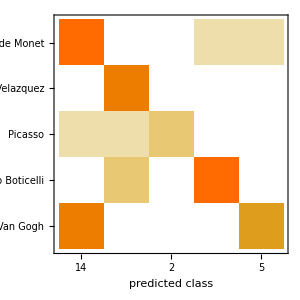

```mathematica
cmeasurements["Accuracy","Uncertainty"-> True]
cmeasurements["ConfusionMatrixPlot"]
```

It can be seen that the classifier confuses Vincent Van Gogh with Claude Monet, the most closely related styles from the five presented, even though Post-Impressionism was a reaction to it’s predecessor movement, specially regarding the use of light an color in natural environments. The classifier and machine learning algorithms does not know this, but it may associate some of the recursive themes in both movements.

If we used the classifier function with van Gogh’s “The Yellow House” we would probably see Monet Van Gogh and Claude Monet as the two most probable ones.

```mathematica
cfunction[-Graphics-,"Probabilities"]
```

<|Claude Monet→0.356509,Diego Velazquez→0.107657,Picasso→0.123233,Sandro Boticelli→0.172911,Vincent Van Gogh→0.239691|>

We could apply the classifier function to any painting or image that is not in the training set. For instance classifying a picture of myself would result in the a classification that associates to either Van Gogh, Diego Velazquez or Picasso. In my defense , given I may not look like the distorted and abstract figures Picasso painted, this classification could be due to the mix of color of the image, which would be more closely related to these painters artwork.

```mathematica
cfunction[-Graphics-,"Probabilities"]
```

<|Claude Monet→0.133087,Diego Velazquez→0.262512,Picasso→0.164959,Sandro Boticelli→0.189694,Vincent Van Gogh→0.249749|>

## Feature Extraction and Space Plot

Built-in functions that relate more to unsupervised learning can be used to see how paintings are separated depending on features extracted by different algorithms. For instance one could extract different features from a training set represented as a vector or finite list of values.

```mathematica
fextraction=FeatureExtraction[Keys@trainingset]
```

FeatureExtractorFunction[…]

Now we can apply this function to an image from the same set and see how the function generates a set of values in a large vector or list.

```mathematica
Keys@trainingset[[2]]
fextraction[%]
```

-Graphics-

{0.202103,-0.733754,2.0958,2.57807,-3.22793,-1.43839,1.95378,0.584498,-1.60692,-2.17092,1.71617,-0.0236894,-1.48702,1.12738,0.483642,1.71855,1.92775,2.25726,-1.96038,-2.18588,-0.126192,0.628503,-2.6034,-0.305962,-1.93697,-0.447902,-2.08845,0.34931,-0.607514,-0.794619,-1.45528,-3.2935,-0.539509,-0.706958,-1.85812,0.204078,-2.33957,-1.98729,0.247778,1.19685,-0.449393,0.710666,0.611433,-0.402236,-2.03849,0.167111,-1.04724,-0.964881,-0.848679,-0.740706,0.310831,0.77787,-0.608025,0.0666998,0.6959,0.662057,-0.0918654,0.92175,0.17525,-1.05648,0.683835,-0.511319,-0.565564,0.686877,0.120122,-1.48967,-0.75196,-0.908499,-0.244286,0.210122,0.0493451,-0.378953,0.721876,1.1739,0.381689,-0.273151,-0.0254468,0.376455,-0.820671,0.0116858,-0.213607,0.268945,-0.898272,0.874502,0.615277,-0.292168,0.810885,0.331247,0.718004,0.180649,-0.544923,0.310576,-0.796934,0.216833,-0.073843,0.114862,0.766284,0.149463,0.110953,-0.262915,-0.810774,-0.146327,0.306214,-0.683706,-0.167249,-0.0908718,-0.753933,-0.125636,-0.612884,0.383824,-0.252007,0.35203,0.131353,0.4145,-0.281366,0.173565,0.00541317,0.76006,-0.188673,-0.0420009,0.491002,0.212411,-0.340326,-0.160273,-0.331853,0.260473,-0.231578,-0.222442,-0.270331,0.647389,-0.095078,0.00632419,0.0179398,0.12854,-0.197936,0.5011,-0.431592,0.0474545,0.0738695}

We can also visualize this parametrization of the features in the images by a space plot.

```mathematica
Iconize[{LabelingFunction->(Callout[ImageResize[#,200],Automatic]&)}]
```

```mathematica
FeatureSpacePlot[Keys@trainingset,ImageSize->Large,]
```

-Graphics-

As expected we can see groups of paintings from the same artist closer together. Alternatively, Impressionist paintings and landscapes can be seen to be on the opposite side and edge of those from portraits from the Baroque and Renaissance period.

To be able to see the different artist the feature Space Plot know will show points with a label of the first letter of the painter name.

```mathematica
Iconize[{ImageSize->Large,
LabelingFunction->(With[{letter=StringTake[trainingset⟦#2⟦2⟧,2⟧,1]},Style[Text[letter],letter/.letterToColor]]&)
,PlotStyle->Opacity[0.5]}]
```

```mathematica
letterToColor=Thread[StringTake[#,{1}]&/@paintersList->colors];
FeatureSpacePlot[Keys[trainingset],]
```

-Graphics-

Similar to our first plot it can be seen how artists from the Baroque and the Renaissance are closer together in the plot, while Monet and Van Gogh are mixed together, again due to a similarity in style.

## Search

This code uses the feature extraction tools applied before to generate a function that, in this case, finds the image with the  nearest features. This could be though of as the shortest distance between two vectors in a multidimensional space.

```mathematica
searchdataset=Keys@trainingset;
nearestf=FeatureNearest[searchdataset]
```

NearestFunction[…]

Again we can apply it to a picture of myself and see the resemblance.

```mathematica
First@nearestf[-Graphics-]
```

-Graphics-

Following the link, you could also upload an image of yourself or even one of your paintings, in the following API deployed to the cloud. You can see what painting from 5 of the most famous painters in history has the nearest features.

```mathematica
CloudDeploy[TestF=FormFunction[{"l"->"Image"},First@nearestf[#l]&]
]
```

CloudObject[https://www.wolframcloud.com/objects/d6f58362-fd48-4130-8b06-0e2da8ef5378]

## Further explorations

Recent articles show studies of how machine learning algorithms differentiate between various styles of painting and movements in art history. It is quite interesting to understand how the algorithms differentiate and classify artworks. The tools in the Wolfram Language could be useful for this purpose.

https://arxiv.org/pdf/1801.07729.pdf

https://arxiv.org/abs/1706.07068

## Author contact information

Diego Gutierrez Coronel

06/28/2018

dgutie10@hawk.iit.edu

(We recommend using your wolfram ID, but any address where you would like to be contacted about this publication should work.)